# Problem 1

## Discussion

We model the spread of Covid-19 using simple SIR (Susceptible-Infected-Recovered) model. The model consists of three differential equations and examines how an infected population spreads the virus to susceptible population which transforms into a recovered population. 

The basic assumptions of the model we discuss here are 
1. No deaths 
2. No Births or Migration 
3. Stable Population 

We take time as our independent variable and see how the spread evolve with time among our population. The dependent variables are S (number of susceptible individuals), I (number of infected individuals), and R (number of recovered individuals). We normalize our dependent variables for simplicity. The scale runs from 0 (representing a zero population) to 1 (representing the full population).

lets start with defining our model equations.  

The first equation describes how the susceptible population changes over time. Because we start with a susceptible population of 1 which decreases over time, we can assume the rate of change will be negative. We subtract the recovered portion  of population.

The second equation describes how the infected population changes over time. It has two terms. The first term is the same as the right hand side of the previous equation, except the sign is now positive. 

 The Third equation describes how the recovered population changes over time. The right hand side is the same as the last term of the previous equation. It represents the transition of infected cases to recovered cases

```mathematica
β = 0.05; α = 0.5; γ = 0.00;
equationS=s'[t]==-α  s[t] i[t] - γ  r[t] ;
equationI=i'[t]== α  s[t]i[t]-β i[t];
equationR=r'[t]==β i[t] -  γ  r[t];
```

The susceptible population starts near 1, with almost everyone being susceptible. It drops over time. The infected population starts with a positive small value near 0. The recovered population starts at 0, with no one having recovered. It increases over time. At any given time  S + I + R  = 1, because the sum represents the full scaled population which is 1. Each infected individual is assumed to spread its disease to α  new individuals each day. If α is high the disease will spread faster.

We also need  to specify initial values at  t=0  for the susceptible, infected, and recovered population. Also we need a small non-zero value for the initial infected population, so we set it to 0.0001 and  set the initial value for the susceptible population to 0.9999. And we will set the initial recovered population to 0.

We avoided using capital letters for variables as it usually reserved for build-in Mathematica variables like I being for complex number symbol.

```mathematica
solution=NDSolve[{equationS,equationI,equationR,s[0]==0.99999,i[0]==0.00001,r[0]==0.0000},{s,r,i},{t,150}];
```

Get the individual solutions for S, I, and R

```mathematica
solutionS=First[s/.solution];
solutionI=First[i/.solution];
solutionR=First[r/.solution];
```

We can plot the results. In our plot, the blue line represents the susceptible population over time, red is infected, and green is recovered:

The plot when we assume that γ = 0 which means that individuals gets lifetime immunity after
recovery.

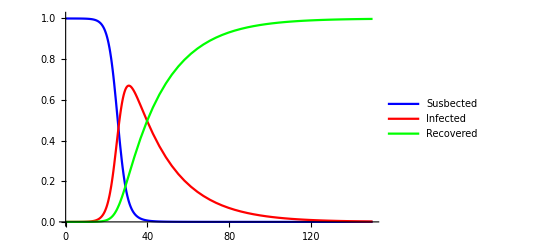

```mathematica
Plot[{
solutionS[t],
solutionI[t],
solutionR[t]
},{t,0,150},
PlotRange->{0,1.01},
PlotStyle->{Blue,Red,Green},PlotLegends-> {"Susbected","Infected","Recovered"}
]
```

We want to make sure that their sum is one so we plot them as follows:

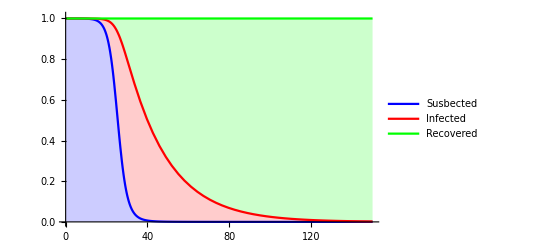

```mathematica
Plot[{solutionS[t],solutionS[t]+solutionI[t],solutionS[t]+solutionI[t]+solutionR[t]},{t,0,150},PlotRange->{0,1.01},Filling->{1->Axis,2->{1},3->{2}},PlotStyle->{Blue,Red,Green},PlotLegends-> {"Susbected","Infected","Recovered"}]
```

Now we want to know what happens if we assume there is partial immunity with γ = 0.04. Which means we assume that the average recovery time is 25 days.

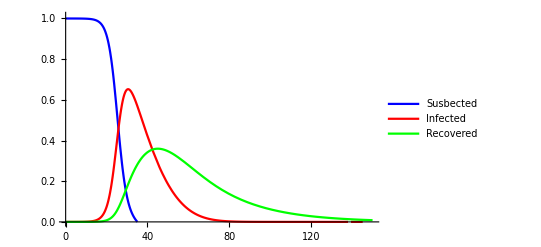

```mathematica
Plot[{
solutionS[t],
solutionI[t],
solutionR[t]
},{t,0,150},
PlotRange->{0,1.01},
PlotStyle->{Blue,Red,Green},PlotLegends-> {"Susbected","Infected","Recovered"}
]
```